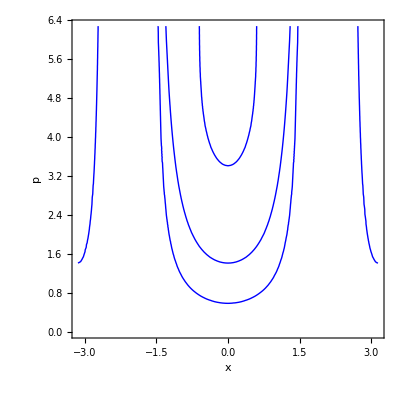

```mathematica
ContourPlot[4 (1-p Cos[x])^2 (Cos[x]^2+(2-p Cos[x])^2 Sin[x]^2)-p^2 Cos[x]^2 (2-p Cos[x])^2==0,{x,-Pi,Pi},{p,0,2 Pi},ContourStyle->{Thick,Blue},FrameLabel->{"x","p"}]
```

```mathematica
Clear[p,equ,h]
equ[p_,x_]:=4 (1-p Cos[x])^2 (Cos[x]^2+(2-p Cos[x])^2 Sin[x]^2)-p^2 Cos[x]^2 (2-p Cos[x])^2
h[p_,x_]:=-2 Cos[x]-2 (1-p Cos[x])/(p (2-p Cos[x]))-p Sin[x]^2 (1+(1-p Cos[x])^2)/(p Cos[x])^2
dx=0.01
(*2 (1-p Cos[x])/(p Cos[x]))*)
(*(1+(1+2 (1-p Cos[x])/(p Cos[x]))^2)==2(1+(1-p Cos[x])^2)/(p Cos[x])^2*)
```

0.01

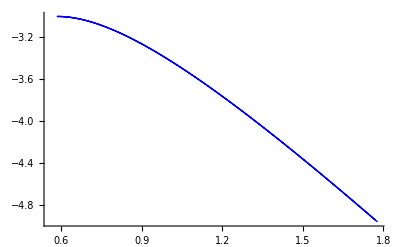

```mathematica
x=-Pi/2;
Sols1plus={};

While[x<Pi/2,sol=Solve[{equ[p,x]==0,p>2-Sqrt[2]},p,Reals];
If[sol≠{},AppendTo[Sols1plus,{x,Flatten[p/.sol][[1]]}]];
x+=dx]

par1plus={};
For[k=1,k≤Length[Sols1plus],k++,{xx,pp}=Sols1plus[[k]];
If[Max[pp,Abs[h[pp,xx]]]<5,AppendTo[par1plus,{pp,h[pp,xx]}]]]
ListLinePlot[par1plus,PlotStyle->{Thick,Blue}](*,AxesStyle->Black,ImageSize->Full]*)
```

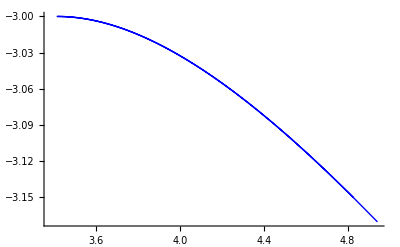

```mathematica
x=-Pi/2;
Sols1minus={};

While[x<Pi/2,sol=Solve[{equ[p,x]==0,p>2+Sqrt[2]},p,Reals];
If[sol≠{},AppendTo[Sols1minus,{x,Flatten[p/.sol][[1]]}]];
x+=dx]
par1minus={};
For[k=1,k≤Length[Sols1minus],k++,{xx,pp}=Sols1minus[[k]];
If[Abs[h[pp,xx]+3]<0.7&&pp<4.95,AppendTo[par1minus,{pp,h[pp,xx]}]]]
ListLinePlot[par1minus,PlotStyle->{Thick,Blue}]
```

```mathematica
x=-Pi/2;
Sols2={};

While[x<Pi/2,sol=Solve[{equ[p,x]==0,p>Sqrt[2]-0.5,p<Sqrt[2]+0.5},p,Reals];
If[sol≠{},AppendTo[Sols2,{x,Flatten[p/.sol][[1]]}]];
x+=dx]
par2={};
For[k=1,k≤Length[Sols2],k++,{xx,pp}=Sols2[[k]];
If[Abs[h[pp,xx]+1]<0.55,AppendTo[par2,{pp,h[pp,xx]}]]]
```

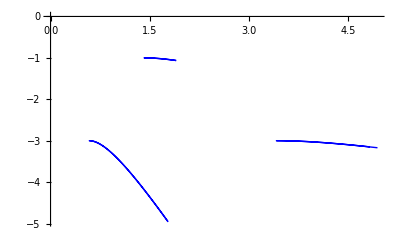

```mathematica
ListLinePlot[{par1plus,par1minus,par2},PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Blue}}]
```

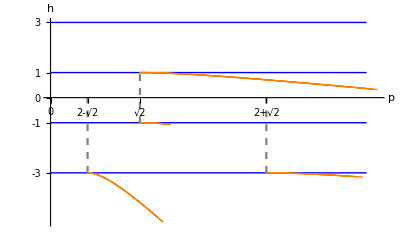

```mathematica
x=Pi/2;
Sols3={};

While[x<3Pi/2,sol=Solve[{equ[p,x]==0,p>2-Sqrt[2],p<5.5},p,Reals];
If[sol≠{},AppendTo[Sols3,{x,Flatten[p/.sol][[1]]}]];
x+=dx]
par3={};
For[k=1,k≤Length[Sols3],k++,{xx,pp}=Sols3[[k]];
If[Max[pp,Abs[h[pp,xx]]]<15,AppendTo[par3,{pp,h[pp,xx]}]]]
ListLinePlot[{Thread[List[Range[0,5.5],-3&/@Range[0,5.5]]],Thread[List[Range[0,5.5],-1&/@Range[0,5.5]]],Thread[List[Range[0,5.5],1&/@Range[0,5.5]]],Thread[List[Range[0,5.5],3&/@Range[0,5.5]]],par1plus,par1minus,par2,par3,Thread[List[2-Sqrt[2]&/@Range[-3,0],Range[-3,0]]],Thread[List[Sqrt[2]&/@Range[-1,1],Range[-1,1]]],Thread[List[2+Sqrt[2]&/@Range[-3,0],Range[-3,0]]]},PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Blue},{Thick,Blue},{Thick,Orange},{Thick,Orange},{Thick,Orange},{Thick,Orange},{Dashed,Gray},{Dashed,Gray},{Dashed,Gray}},Ticks->{{0,2-Sqrt[2],Sqrt[2],2+Sqrt[2]},{-3,-1,0,1,3}},TicksStyle->Directive[Black,14,FontFamily->"Computer Modern"],AxesLabel->{Style["p",FontFamily->"Computer Modern",FontSize->14],Style["h",FontFamily->"Computer Modern",FontSize->14]},AxesStyle->Black,ImageSize->Full]
```

```mathematica
ToExpression["\\omega^2",TeXForm]
```

ω^2